# Práctica 2 Autómatas Celulares

## Autores: Aitana Menárguez Box e Iñaki Diez Lambies

## Parte 2 - Reconocedor de lenguajes

#### Ejercicio 1

```mathematica
Ej1[afd_]:=Module[{q,e,d,q0,F, s,f,sp,aux,i },
q=afd[[1]];e=afd[[2]];d=afd[[3]];
q0=afd[[4]];F=afd[[5]];
s=Union[q,e];sp=F;
f=d; 
aux=Tuples[{q,q}]; 
For[i=1,i≤Length[aux],i++,
AppendTo[aux[[i]],aux[[i]][[2]]];
AppendTo[f,aux[[i]]];
];
aux=Tuples[{e,e}];
For[i=1,i≤Length[aux],i++,
AppendTo[aux[[i]],aux[[i]][[2]]];
AppendTo[f,aux[[i]]];
];
Return [{s,f,sp}];
]
```

```mathematica
afd1={{q,p,r},
{a,b},
{{q,a,p},{q,b,r},{p,a,r},{p,b,q},{r,a,r},{r,b,r}},
{q},
{r}};
```

```mathematica
ac1=Ej1[afd1]
```

{{a,b,p,q,r},{{q,a,p},{q,b,r},{p,a,r},{p,b,q},{r,a,r},{r,b,r},{q,q,q},{q,p,p},{q,r,r},{p,q,q},{p,p,p},{p,r,r},{r,q,q},{r,p,p},{r,r,r},{a,a,a},{a,b,b},{b,a,a},{b,b,b}},{r}}

#### Ejercicios 2 y 3

```mathematica
Ej2[x_List,ac_,q_]:=Module[{s,f,sp,resu,des,sigDes, aux},
s=ac[[1]];f=ac[[2]];sp=ac[[3]]; des=x;
resu={};
AppendTo[resu,des];
sigDes=siguienteDes[Prepend[des,q],f];
While[ToString[des] !=ToString[ sigDes], 

des = sigDes;
sigDes= siguienteDes[Prepend[sigDes,q],f];
AppendTo[resu, sigDes];
];
ArrayPlot[resu,ColorRules->{a->Red,b->Blue,q->Yellow,p->Purple,r->Green}] 
(*
Return[MemberQ[sp, des[[-1]]] ](* Si todos los estados de la descripción son estados finales, devolver True *)
*)

]
```

```mathematica
siguienteDes[des_,f_]:=Module[{nDes,i,t},
nDes={};
For[i=2,i≤Length[des],i++,
t=Flatten[Cases[f,{des[[i-1]],des[[i]],_}]];
AppendTo[nDes,t[[3]]]
];
Return[nDes]
]
```

```mathematica
ac = {{a,b,p,q,r},{{q,a,p},{q,b,r},{p,a,r},{p,b,q},{r,a,r},{r,b,r},{q,q,q},{q,p,p},{q,r,r},{p,q,q},{p,p,p},{p,r,r},{r,q,q},{r,p,p},{r,r,r},{a,a,a},{a,b,b},{b,a,a},{b,b,b}},{r}};
```

{q,a,p,q,b,r,p,a,r,p,b,q,r,a,r,r,b,r,q,q,q,q,p,p,q,r,r,p,q,q,p,p,p,p,r,r,r,q,q,r,p,p,r,r,r,a,a,a,a,b,b,b,a,a,b,b,b}

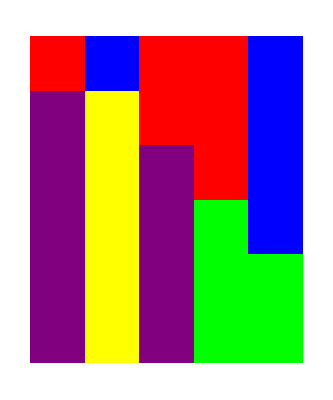

```mathematica
Ej2[{a,b,a,a,b},ac,q]
```